```mathematica
SetDirectory[NotebookDirectory[]];
file="../build/0.h5";
```

```mathematica
Keys[Import[file,"/0"]]
```

{TOV/Lambda,TOV/M,TOV/R,TOV/Rqm,TOV/cs2_cent,TOV/e_cent,TOV/mu_cent,TOV/n_cent,TOV/p_cent,TOV/stab,params/cs2PTl,params/cs2PTr,params/dn,params/ePTl,params/muPT,params/nPTl,params/nbranches,params/pCET,params/pGW,params/pM,params/pPQCD,params/pPT,params/pXray,params/ptot,EOSext/cs2,EOSext/e,EOSext/mu,EOSext/n,EOSext/p,EOS/cs2,EOS/e,EOS/mu,EOS/n,EOS/p,TOVext/Lambda,TOVext/M,TOVext/R,TOVext/Rqm,TOVext/cs2_cent,TOVext/e_cent,TOVext/mu_cent,TOVext/n_cent,TOVext/p_cent,TOVext/stab}

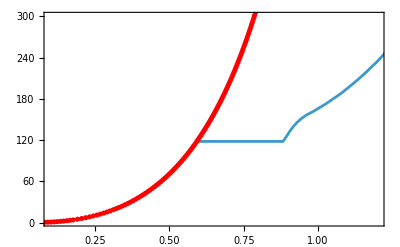
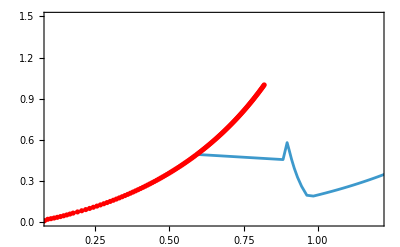
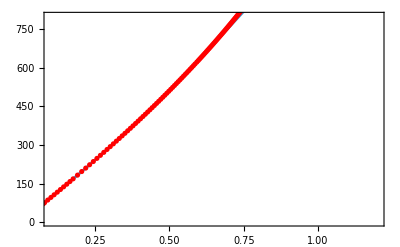
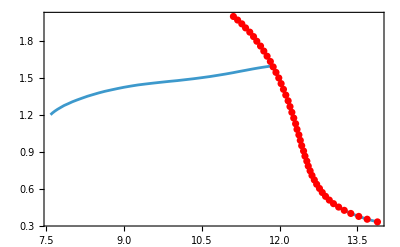

```mathematica
id="1";
n=Import[file,id<>"/EOS/n"];
p=Import[file,id<>"/EOS/p"];
e=Import[file,id<>"/EOS/e"];
R=Import[file,id<>"/TOV/R"];
M=Import[file,id<>"/TOV/M"];
cs2=Import[file,id<>"/EOS/cs2"];
ne=Import[file,id<>"/EOSext/n"];
pe=Import[file,id<>"/EOSext/p"];
ee=Import[file,id<>"/EOSext/e"];
RRe=Import[file,id<>"/TOVext/R"];
Me=Import[file,id<>"/TOVext/M"];
cs2e=Import[file,id<>"/EOSext/cs2"];
{Show[ListPlot[Thread[{n,p}],Joined->True],ListPlot[Thread[{ne,pe}],PlotStyle->Red],PlotRange->{{0.1,1.2},{1,300}},Frame->True],Show[ListPlot[Thread[{n,cs2}],Joined->True],ListPlot[Thread[{ne,cs2e}],PlotStyle->Red],PlotRange->{{0.1,1.2},{0,1.5}},Frame->True],Show[ListPlot[Thread[{n,e}],Joined->True],ListPlot[Thread[{ne,ee}],PlotStyle->Red],PlotRange->{{0.1,1.2},{1,800}},Frame->True],
Show[ListPlot[Thread[{R,M}],Frame->True,Joined->True],ListPlot[Thread[{RRe,Me}],Frame->True,PlotStyle->Red],PlotRange->All]}
```